```mathematica
DateString[]
$Version
```

Tue 21 Mar 2023 11:29:29

13.2.0 for Microsoft Windows (64-bit) (November 18, 2022)

## Lecture 06 edited by Chi-Ok Hwang, originally made by Dr. 전 경원

[1] S. Wolfram, An Elementary Introduction to the Wolfram Language, 2nd ed. Wolfram Media, Inc., 2017.

-Graphics-

Chapters with * marks are optional. We may skip those chapters depending on the progress.

### 29 More about Pure Functions

29 More about Pure Functions

```mathematica
Table[If[i==j,x,i*j],{i,5},{j,5}]
```

{{x,2,3,4,5},{2,x,6,8,10},{3,6,x,12,15},{4,8,12,x,20},{5,10,15,20,x}}

```mathematica
Table[If[i==j,x,i*j],{i,5},{j,5}]//Grid
```

x | 2 | 3 | 4 | 5
2 | x | 6 | 8 | 10
3 | 6 | x | 12 | 15
4 | 8 | 12 | x | 20
5 | 10 | 15 | 20 | x

Array commands

```mathematica
Array[f,10]
Array[f,{3,2}] // Grid
```

{f[1],f[2],f[3],f[4],f[5],f[6],f[7],f[8],f[9],f[10]}

f[1,1] | f[1,2]
f[2,1] | f[2,2]
f[3,1] | f[3,2]

SlotSequence

```mathematica
f[x,#,y,#]&  [a]
f[x,##,y,##]&[a,b,c,d]
f[##2]&[a,b,c,d]
```

f[x,a,y,a]

f[x,a,b,c,d,y,a,b,c,d]

f[b,c,d]

```mathematica
Array[If[#1==#2,x,#1*#2]&,{5,5}]//Grid
```

{f[1],f[2],f[3],f[4],f[5],f[6],f[7],f[8],f[9],f[10]}

x | 2 | 3 | 4 | 5
2 | x | 6 | 8 | 10
3 | 6 | x | 12 | 15
4 | 8 | 12 | x | 20
5 | 10 | 15 | 20 | x

```mathematica
NestList[f,x,5]
```

{x,f[x],f[f[x]],f[f[f[x]]],f[f[f[f[x]]]],f[f[f[f[f[x]]]]]}

```mathematica
FoldList[f,x,{1,2,3,4,5}]
```

{x,f[x,1],f[f[x,1],2],f[f[f[x,1],2],3],f[f[f[f[x,1],2],3],4],f[f[f[f[f[x,1],2],3],4],5]}

```mathematica
FoldList[10 #1+#2&,{8,7,6,1,2,3,9,8,7}]
```

{8,87,876,8761,87612,876123,8761239,87612398,876123987}

Picky exercises: 2, +1

```mathematica
Graphics3D[{RGBColor[#/5],Opacity[.8],Cuboid[#,#+.8]}&/@Tuples[Range[5],3]]
```

-Graphics3D-

```mathematica
Plus[4+5]
```

9

```mathematica
Plus@4-5+3
```

2

```mathematica
Sin[(Plus@@4-5)/3]
```

-Sin[1/3]

```mathematica
Manipulate[Graphics3D[{Hue[#[[3]]],Opacity[0.2],Cuboid[#,#+0.8]}&/@(Append[#,Sin[(Plus@@#-k)/3]]&/@Tuples[Range[10],2])],{k,1,100}]
```

### 30 Rearranging Lists

30 Rearranging Lists

Transpose

```mathematica
{{1,2},{3,4},{5,6},{7,8},{9,10}} // Grid
```

1 | 2
3 | 4
5 | 6
7 | 8
9 | 10

```mathematica
Transpose[{{1,2},{3,4},{5,6},{7,8},{9,10}}] // Grid
```

1 | 3 | 5 | 7 | 9
2 | 4 | 6 | 8 | 10

Thread

```mathematica
Thread[{1,3,5,7,9}->{2,4,6,8,10}]
```

{1→2,3→4,5→6,7→8,9→10}

Partition

```mathematica
Partition[Range[12],3]
```

{{1,2,3},{4,5,6},{7,8,9},{10,11,12}}

```mathematica
Partition[Characters["An array of text made in the Wolfram Language"],9] // Grid
```

A | n |   | a | r | r | a | y |  
o | f |   | t | e | x | t |   | m
a | d | e |   | i | n |   | t | h
e |   | W | o | l | f | r | a | m
  | L | a | n | g | u | a | g | e

```mathematica
Grid[Partition[Characters["An array of text made in the Wolfram Language"],9],Frame->All]
```

A | n |   | a | r | r | a | y |  
o | f |   | t | e | x | t |   | m
a | d | e |   | i | n |   | t | h
e |   | W | o | l | f | r | a | m
  | L | a | n | g | u | a | g | e

```mathematica
Partition[Characters["An array of text made in the Wolfram Language"],9]
```

{{A,n, ,a,r,r,a,y, },{o,f, ,t,e,x,t, ,m},{a,d,e, ,i,n, ,t,h},{e, ,W,o,l,f,r,a,m},{ ,L,a,n,g,u,a,g,e}}

Picky exercises: 6, 8, 10, 13, 16, 17, 18, 20, 21, +1, +6, +9, +13

```mathematica
StringJoin@Riffle[StringSplit["Tweet a Program"],"-"]
```

Tweet-a-Program

### 31 Parts of Lists

31 Parts of Lists

Part lets you pick out an element of a list.

```mathematica
Part[{a,b,c,d,e,f,g},2]
{a,b,c,d,e,f,g}[[2]]
{a,b,c,d,e,f,g}[[-2]]
```

```mathematica
{a,b,c,d,e,f,g}[[{2,4,5}]]                     (* You can ask for a list of parts by giving a list of part numbers. *)
```

;; lets you ask for a span or sequence of parts.

```mathematica
{a,b,c,d,e,f,g}[[2;;5]]
```

Take

```mathematica
Take[{a,b,c,d,e,f,g},4]
Take[{a,b,c,d,e,f,g},-2]
```

Drop

```mathematica
Drop[{a,b,c,d,e,f,g},-2]
```

{a,b,c,d,e}

Let’s now talk about lists of lists, or arrays. Each sublist acts as a row in the array.

```mathematica
{{a,b,c},{d,e,f},{g,h,i}}//Grid
{{a,b,c},{d,e,f},{g,h,i}}[[2]]                      (* Pick out the second sublist,corresponding to the second row,in the array:  *)
```

```mathematica
{{a,b,c},{d,e,f},{g,h,i}}[[2,1]]                    (* This picks out element 1 on row 2:  *)
```

```mathematica
{{a,b,c},{d,e,f},{g,h,i}}[[All,1]]                 (* Pick out the first column,by getting element 1 on all rows:  *)
```

Position  finds the list of positions at which something appears.

ReplacePart lets you replace parts of a list:

Sometimes one wants particular parts of a list to just disappear. One can do this by replacing them with Nothing.

```mathematica
ReplacePart[{a,b,c,d,e,f,g},{1->Nothing,3->Nothing}]
```

```mathematica
{b,d,e,f,g}
ReplacePart[{a,b,c,d,e,f,g},{1->Nothing,2->Nothing}]
```

{b,d,e,f,g}

{c,d,e,f,g}

TakeLargest, TakeSmallest

```mathematica
TakeLargest[Range[20],5]
```

TakeLargestBy, TakeSmallestBy take elements based on applying a function.

```mathematica
TakeLargestBy[Array[RomanNumeral,100],StringLength,5]
```

Picky exercises: 3, 6, 7, 10, 11

### 32 Patterns

32 Patterns

```mathematica
Patterns are a fundamental concept in the Wolfram Language.The pattern _ (read “blank”) stands for anything.
```

MatchQ tests whether something matches a pattern

```mathematica
MatchQ[{a,x,b},{_,x,_}]
MatchQ[{a,x,b},{_,x,_}]
```

True

True

Cases  lets you pick out all the elements (“cases”) in a list that match a particular pattern.

```mathematica
Cases[{{a,a},{b,a},{a,b,c},{b,b},{c,a},{b,b,b}},{_,_}]
```

{{a,a},{b,a},{b,b},{c,a}}

One of the many uses of patterns is to define replacements. /. (“slash dot”) performs a replacement.

```mathematica
{a,b,a,a,b,b,a,b}/.b->Red
```

Picky exercises: 6

### 33 Expressions and Their Structure

33 Expressions and Their Structure

FullForm shows you the internal form of any symbolic expression.

```mathematica
FullForm[{{a,b},{c,d}}]
```

List[List[a,b],List[c,d]]

What are the ultimate building blocks of symbolic expressions? They’re called atoms (after the building blocks of physical materials). The main kinds of atoms are numbers, strings and symbols. 

Things like x, y, f, Plus, Graphics and Table are all symbols. Every symbol has a unique name. Sometimes it’ll also have a meaning attached. Sometimes it’ll be associated with evaluation. Sometimes it’ll just be part of defining a structure that other functions can use. But it doesn’t have to have any of those things; it just has to have a name.

A crucial defining feature of the Wolfram Language is that it can handle symbols purely as symbols—“symbolically”—without them having to evaluate, say to numbers.

```mathematica
x+x+x+2 y+y+x
```

9+4 x

```mathematica
Clear[y]
x+x+x+2 y+y+x
```

4 x+3 y

TreeForm: You can display an expression as a tree using TreeForm.

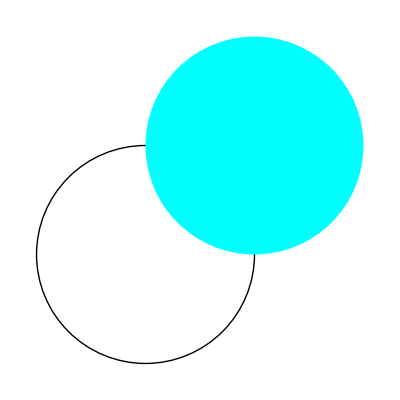

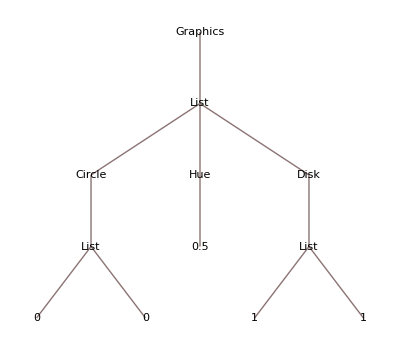

```mathematica
Graphics[{Circle[{0,0}],Hue[1.5],Disk[{1,1}]}]
TreeForm[Graphics[{Circle[{0,0}],Hue[0.5],Disk[{1,1}]}]]
```

In f[x,y], f is called the head of the expression. x and y are called arguments. The function Head extracts the head of an expression.

```mathematica
Head[{x,y,z}]
Head[{x,y,z}]
```

_Integer is a pattern that matches only objects with head Integer:

```mathematica
Cases[{x,y,3,4,z,6,7},_Integer]
```

Length does not care what the head of an expression is; it just counts arguments:

```mathematica
Length[f[x,y,z]]
```

Basic objects: expressions, atoms, symbols, ...

Expressions

Symbols

Contexts

Atomic Objects

Numbers

Character Strings

Picky exercises: 5

```mathematica
MapApply[f,{{a,b},{c,d}}]
f@@@{{a,b},{c,d}}
```

{f[a,b],f[c,d]}

{f[a,b],f[c,d]}

```mathematica
Plus@@@{{a,b,c,d},{1,2,3,4},{e,f,5,6}}
```

{a+b+c+d,10,11+e+f}

```mathematica
MapApply[Plus,{{a,b,c,d},{1,2,3,4},{e,f,5,6}}]
```

{a+b+c+d,10,11+e+f}

```mathematica
GeoGraphics[
{EdgeForm[Black],{GeoStyling[{"Image",#2}],Polygon[#1]}&@@@EntityValue[EntityClass["Country","Asia"],{"Entity","Flag"}]},GeoBackground->"StreetMapNoLabels",GeoProjection->"Mollweide",GeoRange -> "World"]
```

-Graphics-

### 34 Associations

34 Associations

```mathematica
Associations are a kind of generalization of lists,in which every element has a key as well as a value.
```

Counts

```mathematica
Counts[{a,a,b,c,a,a,b,c,c,a,a}]
```

Picky exercises: 3, 4, 5

### 35 Natural Language Understanding *

35 Natural Language Understanding

Picky Exercises: 6, 7, 10 , 11, 12, 13

### 36 Creating Websites and Apps *

36 Creating Websites and Apps

Picky Exercises: 2, +1

### 37 Layout and Display *

37 Layout and Display *

Frame

```mathematica
Framed[2^100,Background->LightYellow,FrameStyle->LightGray]
```

Labeled

```mathematica
Labeled[Style[2^100,Background->Yellow],Style["a big number",Italic,Orange]]
```

```mathematica
ListPlot[{Labeled[1,"one"],Labeled[2,"two"],Labeled[3,Pink],Labeled[4,Yellow],5,6,7}]
```

Callout: Labeled indicates something by putting a label right next to it. It’s often nice instead to use “callouts”, that have little lines pointing to whatever they’re referring to. You can do this by using Callout rather than Labeled.

```mathematica
ListPlot[Table[Callout[Prime[n],Prime[n]],{n,15}]]
```

Style:

```mathematica
PieChart[{Style[3,Red],Style[2,Green],Style[1,Yellow],1,2}]
```

Tooltip

```mathematica
Tooltip generates interactive tooltips that show themselves when the mouse hovers over them.
```

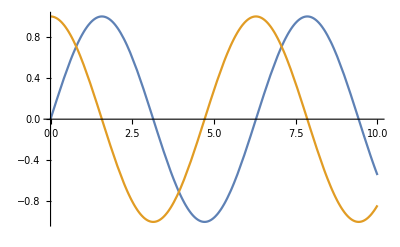

```mathematica
Plot[Tooltip[{Sin[x],Cos[x]}],{x,0,10}]
```

Legended

```mathematica
PieChart[{Legended[1,"one"],Legended[2,"two"],Legended[3,Pink],Legended[4,Yellow],2,2}]
```

-Graphics-

Picky Exercises: 1, 3, 4, 5, 7, 8

### 38 Assigning Names to Things

38 Assigning Names to Things

Particularly when you’re doing quick experiments in the Wolfram Language, it’s often convenient to use % to refer to the result of your most recent computation.

```mathematica
Range[10]
%^2
```

{1,2,3,4,5,6,7,8,9,10}

{1,4,9,16,25,36,49,64,81,100}

If you expect to refer to a result later, you can assign it a name.

```mathematica
range10=Range[10]
range10^2
```

{1,2,3,4,5,6,7,8,9,10}

{1,4,9,16,25,36,49,64,81,100}

You can assign a name to the result of a computation even if you never display the result. End your input with ; (semicolon) to avoid seeing the result.

```mathematica
millionlist=Range[1000000];
Total[millionlist]
```

When you assign a name to something, the name will stay until you explicitly clear it.

```mathematica
x=42
x^2
```

```mathematica
y=3
x+y
```

```mathematica
Clear[x]
x+y
```

3+x

Assigning a global value for x, like x=42, is potentially a big deal, because it can affect everything you do in your session (at least until you clear x). Something that’s much safer—and extremely useful—is just to assign a temporary, local value to x, inside a module.

```mathematica
f[x0_]:=Module[{x=x0},While[x>0,x=Log[x]];
 x]
f[2.0]
```

-0.366513

```mathematica
fib[n_]:=Module[{f},f[1]=f[2]=1;
f[i_]:=f[i]=f[i-1]+f[i-2];
f[n]]
fib[5]
```

5

```mathematica
Module[{x=Range[10]},x^2]
x
```

{1,4,9,16,25,36,49,64,81,100}

x

Further Reading about Lexical and Dynamic Scoping

Blocks Compared with Modules

Scope (computer science)

Picky Exercises: 3, 4, 7